# Implementation of Sessie as an Association:

## SSSInitialize, SSSSingleStep, SSSEvolve, SSSDisplay, and SSSInteractiveDisplay all take and/or return an SSS Association ( <|...|> ).

```mathematica
Clear[FromAlpha,ToAlpha,SSSConvert, SSSStrip]; 
FromAlpha[string_String] :=(ToCharacterCode[string]-65);  
ToAlpha[l:{___Integer}] := FromCharacterCode[l+65];

Attributes[s]=Flat;
SSSConvert[string_String] := s @@ FromAlpha[string];
SSSConvert[s[x___]] := ToAlpha[{x}];
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats, using the functions FromAlpha and ToAlpha.";

SSSStrip[x_s] := SSSConvert[x⟦All,1⟧] /; MatrixQ[List@@x]    (* if dim=2, take only 1st component, and convert *)
SSSStrip[x_s] := ""  /; Length[List@@x]==0     (* treat empty string case *) 

SSSStrip::usage="SSSStrip[StyleBox[\"state\",FontSlant->\"Italic\"]] strips out tags from a StyleBox[\"state\",FontSlant->\"Italic\"] given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
Clear[ToCharacterWeights, FromCharacterWeights, StringWeight, RuleSetWeight, RuleSetLength];
ToCharacterWeights[s_String] := (1+FromAlpha[s]);
FromCharacterWeights[l:{___Integer}] := ToAlpha[l-1];
(* Note: To avoid breaking the ruleset (un-)rank functions, avoid the temptation to define:  
ToCharacterWeights[""] = 0;  FromCharacterWeights[{0}]="";  *)
StringWeight[s_String] := Plus @@ ToCharacterWeights[s];
RuleSetWeight[rs_List] := Plus @@ (StringWeight /@ Flatten[rs /. Rule->List]);
RuleSetLength[rs_List] := Plus @@ (StringLength /@ Flatten[rs /. Rule->List]);
```

```mathematica
Clear[myColorOptions,patternPrint,SSSRuleIcon];
myColorOptions[maxColor_Integer (* minimum 1 *) ]:=Sequence[ColorRules->{0->LightGray},
ColorFunction->(Hue[(#-1)/(Max[1,maxColor])]&),ColorFunctionScaling->False];
patternPrint[pattern_,mxClr_Integer,opts___] := ArrayPlot[{{##}}& @@pattern,myColorOptions[mxClr],Mesh->True,opts,ImageSize->{Automatic,20}];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,mxClr_Integer:6,opts___] := Panel[Grid[Map[patternPrint[#,mxClr,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
SSSRuleIcon::usage="SSSRuleIcon[StyleBox[\"rule\",FontSlant->\"Italic\"]StyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"s\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"maxColor\",FontSlant->\"Italic\"]] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```

```mathematica
Clear[SSSNewRule];
SSSNewRule[rulenum_Integer,(rule_Rule | rule_RuleDelayed)] := 
(* the tagged rule created will need valid versions of $SSSConnectionList, $SSSTagIndex, $SSSRulesUsed, and will change them!  It's up to the calling routine to load/unload these globals.  *)
Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@Transpose[{FromAlpha[lhs],ToString@#<>"_"& /@ lhsNames}]];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2=ToString[SSSConvert[rhs] /. n_Integer :> {n,"$SSSTagIndex++"}];
ToExpression[newlhs<>" :> ("<>"AppendTo[$SSSRulesUsed,"<>ToString@rulenum<>"];"<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := Append[MapIndexed[SSSNewRule[First[#2],#1]&,rules],___:>AppendTo[$SSSRulesUsed,0]];
SSSNewRule::usage= 
"SSSNewRule[rule(s)] generates the needed rules for the tagged SSS (sequential substitution system) from the ruleset of rules given in string-format: e.g., \"BA\"→\"ABA\"";
```

```mathematica
Clear[SSSInitialize];
Options[SSSInitialize]={Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSInitialize::usage = "StyleBox[\"variable\",FontSlant->\"Italic\"] = SSSInitialize[ruleset, string, (mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,\nstarting with a ruleset (e.g., {\"BA\"→\"ABA\"}) and an initial state string (e.g., \"BABA\").  The True|False return value indicates whether initialization was successful.\n\nIf omitted, mode defaults to \"Silent\", suppressing the short error or success message.\n\nThe following global variables are reset by this operation:\n\n$SSSNet:\t\t\t\tthe causal network of the current SSS,\n$SSSInDegree:\t\t\tthe list of in-degrees for each node,\n$SSSOutDegreeActual:\t\tthe list of currently found out-degrees for each node,\n$SSSOutDegreePotential:\t\tthe list of maximum possible out-degrees for each node,\n$SSSOutDegreeRemaining:\tthe list of numbers of possible remaining out-connections for each node,\n$SSSConnectionList:\t\tthe current list of all causal network connections,\n$SSSDistance:\t\t\tthe list of minimum distances from the current node back to the starting node.\n$SSSTagIndex:\t\t\tthe current tag index being used,\n$SSSTEvolution:\t\t\tthe complete evolution of the tagged SSS so far,\n$SSSEvolution:\t\t\tthe stripped (tagless) version of $SSSTEvolution,\n$SSSRuleSet:\t\t\tthe ruleset used for creating the SSS,\n$SSSTRuleSet:\t\t\tthe version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,\n$SSSRuleSetWeight:\t\tthe total weight of $SSSRuleSet,\n$SSSRuleSetLength:\t\tthe total length of $SSSRuleSet,\n$SSSRulesUsed:\t\tthe list of rules used\n$SSSCellsDeleted:\t\tthe list of cells in the state string deleted at each step,\n$SSSVerdict:\t\t\tset to \"Dead\" | \"Repeating\" as soon as the future of the SSS becomes clear.";

SSSInitialize[rs:{___Rule},state_String,opts:OptionsPattern[] (* Mode -> Silent | Quiet | Loud *)] :=
Module[{ans=<|"Net"->{},"OutDegreePotential"->{},"OutDegreeRemaining"->{},"OutDegreeActual"-> {},
"InDegree"-> {},"ConnectionList"->{},"Verdict"->"OK", "RulesUsed"->{},"CellsDeleted"->{},
"Distance"->{0}|>}, (* initial setup *)
AssociateTo[ans,{
"MaxColor"->Max[Flatten[{6,ToCharacterWeights /@ Flatten[rs/.Rule->List]}]],
"TagIndex"->StringLength[state]+1,
"TEvolution"->{s@@Transpose[{#,Range[Length[#]]}& @ FromAlpha[state]]},
"Evolution"->{state}, "RuleSet"->rs, "TRuleSet"->SSSNewRule[rs],
"RuleSetWeight"->RuleSetWeight[rs], "RuleSetLength"->RuleSetLength[rs]
}];

{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

Switch[ Last[ans["RulesUsed"]], (* can also test if Length[ans["ConnectionList"]]==0 *)
0,ans["TEvolution"]=Most[ans["TEvolution"]]; (* toss last duplicate entry *)
      ans["Verdict"]="Dead";
      If[ OptionValue[Mode]==Loud,Print["Error: No evolution possible starting from \""<>state<>"\" using ruleset: ",rs]];
      Return[ans (* but already including "Verdict" = Dead *)],
_, AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]]; (* add last entry *)
       If[ OptionValue[Mode]==Loud,Print["Successful initialization of ruleset: ",rs,", evolution: ",ans["Evolution"]]]
];
(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; (* # of cells created by last rule *)
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

ans  (* Return the association created *)
];
```

```mathematica
Clear[SSSSingleStep];
SSSSingleStep::usage=
"SSSSingleStep[sss] performs a single step of the sequential substitution system sss evolution (if not already dead), returning the sss object (which must be created by SSSInitialize first).";

SSSSingleStep[sss_Association] := Module[{ans=sss,cd, ri, pri, rs, prs,len,startingEvents, oda, odr},
If[ans["Verdict"]==="Dead",Return[ans]];  (* if already dead, do nothing, return *)

(* do the actual evolution step *)
{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

If[Last[ans["RulesUsed"]]==0,ans["Verdict"]="Dead"; 
ans["TEvolution"]=Most[ans["TEvolution"]]; 
Return[ans]
];

AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]];

If[!MatchQ[ans["Verdict"],"Repeating"],  (* to limit wasted time, don't do this if the verdict is already in! *)
If[Length[Flatten@Position[ans["Evolution"],Last[ans["Evolution"]]]]>1, ans["Verdict"]="Repeating"]
]; 

(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; 
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

(* now the steps that are only done for non-initial steps, comparing to previous entries in ans["ConnectionList"]: *)
len=Length[ans["ConnectionList"]];
startingEvents=Flatten[If[Length[#]>0,First[First[#]],#]& /@ (Position[ans["ConnectionList"]⟦;;-2⟧,#]& /@ ans["ConnectionList"]⟦-1,1⟧)];
oda=ans["OutDegreeActual"];
oda⟦#⟧++& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeActual"->oda];
odr=ans["OutDegreeRemaining"];
odr⟦#⟧--& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeRemaining"->odr];
AssociateTo[ans,"Net"->Join[ans["Net"],#->len& /@ startingEvents]];           (* add new links to the causal network *)
AssociateTo[ans,"Distance"->Append[ans["Distance"],Min[ans["Distance"]⟦startingEvents⟧]+1]];  (* Find minimum path length of cause nodes, add 1 for path lengths of result nodes *)

ans  (* Return the updated association *)
];
```

```mathematica
Clear[SSSEvolve];
Options[SSSEvolve]={EarlyReturn->False, Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSEvolve[sss_Association,n_Integer/;n>0,opts:OptionsPattern[]] := Module[{ans=sss},
If[OptionValue[EarlyReturn] ,
Do[If[MatchQ[ans["Verdict"], ("Dead"|"Repeating")],Return[ans],ans=SSSSingleStep[ans]],{n}], (* check before each step *)
Do[ans=SSSSingleStep[ans],{n}]   (* just do it *)
];
If[OptionValue[Mode]==Loud,Print[ans["Verdict"]]];
ans
]
```

```mathematica
SSSEvolve::usage="SSSEvolve[sss, n] generates an additional n levels of indicated sss (sequential substitution system), which must have been previously created using SSSInitialize.  Use the option EarlyReturn → True to allow early termination for repeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.)  In Loud mode, prints the current verdict, \"OK\" means none known.  Values of sss updated, with \"Evolution\" containing the tagless SSS, \"ConnectionList\" the updated causal network connection list, etc.  mode can be Silent, Quiet, or Loud.";
```

```mathematica
Clear[SSSDisplay];
Options[SSSDisplay]=
{HighlightMethod->True,RulePlacement->Bottom,Mesh->True,NetSize->{Automatic,400},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,
Max->∞,SSSMax->Automatic,NetMax->Automatic,
Min->1,SSSMin->Automatic,NetMin->Automatic, 
Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
SyntaxInformation[SSSDisplay]={"ArgumentsPattern"->{OptionsPattern[]}};
```

```mathematica
SSSDisplay::usage="SSSDisplay[sss, opts] displays the sequential substitution system sss and/or its causal network.  Use SSS (or SSSInitialize and SSSEvolve) to construct it first.

Options:
\tMin → n cuts off the display before the first n steps of the system.  (Separate values can be specified for SSSMin and NetMin.)
\tMax → n cuts off the display after the first n steps of the system.  (Separate values can be specified for SSSMax and NetMax.)
\tVertexLabels → Automatic (or \"Name\") | \"VertexWeight\" | …  labels vertices by node number or distance from origin, etc.

\tHighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

\tShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

\tSizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

\tNetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, \n\t\twhere NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.";
```

```mathematica
SSSDisplay[sss_Association, opts:OptionsPattern[]] := Module[{HlM,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,mn,netmn,sssmn,hs,start,ev,vrtxs,net,grph,DE},

HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
RP=OptionValue[RulePlacement];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
DE= OptionValue[DirectedEdges];

mx=OptionValue[Max];
If[mx===Automatic,mx=∞];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];

mn=OptionValue[Min];
If[mn===Automatic,mn=1];
sssmn=OptionValue[SSSMin]; 
If[sssmn===Automatic,sssmn=mn];
netmn=OptionValue[NetMin]; 
If[netmn===Automatic,netmn=mn];

start=1;

vrtxs =Annotation[#,VertexWeight->sss["Distance"]⟦#⟧]&/@Range[Max[start,netmn],Min[netmx,Length[sss["Distance"]]]];

net=(Select[sss["Net"],And@@Thread[Max[start,netmn]≤List@@#≤netmx]&] /. n_Integer:>(n+1-start));

(*
If[UD||(DM<∞),net=(net /.nn_Integer:>Subscript[sss["Distance"]⟦nn⟧,Style[nn,Tiny]])];
If[DM<∞,
net=Cases[net,r:Rule[Subscript[_?(#≤DM&),_],Subscript[_?(#≤DM&),_]]:> r];
If[!UD,net=(net /. Subscript[_,Style[n_Integer,_]]:>n)]
];
*)

grph=Graph[vrtxs,net,DirectedEdges->DE];

doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];

If[sss["Verdict"]=="Dead",doGP=doLGP=doTP=doGP3D=False];

cellsToHighlight=Flatten[MapIndexed[{#1,#2⟦1⟧}&,Reverse@(sss["CellsDeleted"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧),{2}],1];
rulesApplied=Reverse@(sss["RulesUsed"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧);

ans = 
ArrayPlot[(FromAlpha/@ (sss["Evolution"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]⟧)),myColorOptions[sss["MaxColor"]],Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied⟦y⟧,{x,y}+.5{-1,1}}),
_,{}]
];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[RP,
Right, Grid[{{ans,SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]}}],
Left, Grid[{{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS],ans}}], 
Bottom|True, Grid[{{ans},{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]}}], 
Top,  Grid[{{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]},{ans}}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[grph,GraphLayout->"SpringElectricalEmbedding",
Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],
VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doLGP,LayeredGraphPlot[grph,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doTP,TreePlot[grph,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center],DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[grph,GraphLayout->"SpringElectricalEmbedding",Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}]
},"  "]]
```

```mathematica
SSS[rs:{___Rule},init_String,n_Integer?Positive,opts___] := Module[{sss},
sss=SSSInitialize[rs,init,Mode->Silent];
If[sss["Verdict"]=!="Dead", 
sss=SSSEvolve[sss,n-1,Sequence@@FilterRules[{opts},Options[SSSEvolve]]]; 
Print@SSSDisplay[sss,Sequence@@FilterRules[{opts},Options[SSSDisplay]]];
];
sss
];
Options[SSS]=Join[Options[SSSEvolve],Options[SSSDisplay]];
SyntaxInformation[SSS]={"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};
```

```mathematica
SSS::usage="SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(Returns a copy of the SSS that can then be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly, looking at its keys, \"Evolution\" and \"Net\", etc.)";
```

```mathematica
Clear[SSSInteractiveDisplay,dynamicLabel];

dynamicLabel[lbl_,max_]:=Dynamic[If[Clock[{1,max,1},max]==lbl,Framed[lbl,Background->Green,RoundingRadius->Scaled[.5]],lbl]];

SetAttributes[SSSInteractiveDisplay,HoldFirst];

SSSInteractiveDisplay[sss_] := With[{mxmx=Max[List @@@ Evaluate[sss]["Net"]]},
Manipulate[
If[Head[vl]===List,vp=Automatic];
If[mx<mn,mx=mn+1];
If[sssmx<sssmn,sssmx=sssmn+1];
If[ntmx<ntmn,ntmx=ntmn+1];
args={Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,RulePlacement->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexSize->vs,
VertexLabels->If[vp===Automatic,vl,Placed[vl,vp]],
DirectedEdges->dir};
SSSDisplay[Evaluate[sss],Flatten[args,1]],
Grid[{{
Control[{{hlm,Number,"HighlightMethod"},{Dot,Frame,Number,None}}],
Control[{{sr,Bottom,"RulePlacement"},{Bottom,Top,Left,Right,None}}],
Control[{{nm,GraphPlot,"NetMethod"},{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D,All}}],
Button["Save these options",
CellPrint[ExpressionCell[Defer[SSSDisplay][Defer[sss],Evaluate[Sequence@@args]],"Input"]];
SelectionMove[InputNotebook[],Previous,Cell];
]
}},Spacings->2],
{args,{},ControlType->None},
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],
Row[{
Control[{{dir,False,"directed"},{False,True}}],"    ",
Control[{{no,False,"NoSSS"},{False,True}}]
}]
},
{Control[{{sssmn,0,"SSSMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{sssmx,mxmx+1,"SSSMax"},0,mxmx+1,1,Appearance->"Labeled"}],"(a NetMethod option)"},{Control[{{ntmn,0,"NetMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{ntmx,mxmx+1,"NetMax"},0,mxmx+1,1,Appearance->"Labeled"}],
Control[{{vs,Automatic,"VertexSize →"},{Automatic,Tiny,Small,Medium,Large,0.8->"Huge"},ControlType->PopupMenu}]
},
{Control[{{ssss,220,"SSSSize"},10,500,Appearance->"Labeled"}],
Control[{{is,350,"ImageSize"},10,500,Appearance->"Labeled"}],Control[{{vl,Automatic,"VertexLabels →"},{Automatic,None,"Name","VertexWeight",
((#->Placed[#,Center,Function[{arg},dynamicLabel[arg,ntmx]]])&/@Range[ntmn+1,ntmx-1])->"Dynamic"},ControlType->PopupMenu}]},
{Control[{{cns,20,"IconSize"},10,50,Appearance->"Labeled"}],Control[{{ns,300,"NetSize"},10,800,Appearance->"Labeled"}],
Control[{{vp,Automatic,"Placed"},
{Automatic,Center,Before,After,Below,Above,Tooltip,StatusArea}}]}
},Alignment->Right,Spacings->2]
]]
SSSInteractiveDisplay::usage="SSSInteractiveDisplay[sss] provides an interactive display of sss and its causal network, with controls for easy adjustment of common options.  Click the button to create a SSSDisplay object with the selected options.";
```

```mathematica
Clear[SSSAnimate];
SSSAnimate[sss_Association, opts:OptionsPattern[{VertexLabels->"Name",SSSDisplay}]] := Module[{g,mn,mx,VL},
{VL,mn,mx}=If[FreeQ[OptionValue[VertexLabels],"VertexWeight"],
{Placed["Name",Center],1,Length[sss["Evolution"]]},
{Placed["VertexWeight",Center],0,Max[sss["Distance"]]}];
g= SSSDisplay[sss,VertexLabels->VL (* override *),opts,
(* defaults: *) NetSize->600,NetMethod->{GraphPlot,NoSSS},VertexSize->Automatic,DirectedEdges->False];
Animate[g /. {
{Disk[__],Text[n,{x_,y_},BaseStyle->"Graphics"] }:> Text[Framed[n,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->10],
{x,y},BaseStyle->"Graphics"],
{Disk[__],Text[m:Except[n,_Integer],{x_,y_},BaseStyle->"Graphics"] }:>Point[{x,y}]
},
{n,mn,mx,1,Appearance->"Labeled",AnimationRate->2,AnimationRunning->True}]];
```

```mathematica
SSSAnimate::usage="SSSAnimate[sss, opts] animates the display of the causal network of the sequential substitution system sss.  Use SSS (or SSSInitialize and SSSEvolve) to construct it first.  Takes all the options of SSSDisplay, with one modification:

VertexLabels → \"Name\" (default) | \"VertexWeight\"  display the vertex name/index or its distance from the origin.";
```

### Universal enumeration and rulesets tests

#### Initial string for a given ruleset: SSSInitialState (defines & uses nextLyndon, deBruijn)

```mathematica
Clear[nextLyndon,deBruijn];
nextLyndon[k_,n_,w_List] := Module[{x=Table[0,{n}],l=Length[w],lastchar=n},
x=w⟦Mod[Range[1,n],l,1]⟧;   (* permute the digits appropriately *)
While[lastchar≥0 && x⟦lastchar⟧==k-1,lastchar--];  (* back up past end trash *)
If[lastchar==0,
{}, (* nothing left, we're done *)
x⟦lastchar⟧++;x⟦;;lastchar⟧  (* increment last digit, return appropriate part *)
]];
deBruijn[k_,n_] := deBruijn[k,n]=Module[{s,d=Divisors[n]},
s=NestWhileList[nextLyndon[k,n,#]&,{0},#≠{}&];
Join @@ Select[s,MemberQ[d,Length[#]]&]
];
```

```mathematica
Clear[SSSInitialState];
SSSInitialState[r_Rule] := Module[{lhs,k,n,chars,s,len},
lhs=First[r];
If[lhs=="",lhs="A"];
chars=Union[Characters [lhs]];
k=Length[chars];
n=StringLength[lhs];
s=deBruijn[k,n]⟦Mod[Range[k^n+n-1],k^n,1]⟧;
StringJoin[s /. Thread[Range[k]-1->chars]]
];
SSSInitialState[rs:{Rule[_,_]...}] := Module[{lhs=First /@ rs,runs,bigruns,full=StringJoin[Union[SSSInitialState /@ rs]],dels},
runs = Union[Flatten[StringJoin /@ Split[Characters[#]]& /@ lhs]]; (* runs of same character existing in lhs *)
bigruns=Last /@ SplitBy[runs,StringTake[#,1]&]; (* biggest run of each character *)
dels=StringJoin[#,StringTake[#,1]]& /@ bigruns; (* next bigger for each character *)
FixedPoint[StringReplace[#,Thread[dels->bigruns]]&,full]  (* keep replacing the too big runs by the max allowed size, stop when no futher change *)
];
```

Should rethink logic!  Short is good, too short is fatal.  This initial state string needs to be long enough and contain enough of the right characters in the right order(s) to be useful for the specified ruleset.

#### Override SSS to use SSSInitialState if no specific initial state is given:

```mathematica
SSS[rs:{___Rule},n_Integer?Positive,opts___] := SSS[rs,SSSInitialState[rs],n,opts]
```

#### Rank / Unrank functions from the reduced enumeration of sequential substitution systems:

It is duplication of effort to have separate functions to go between rank, quinary code (provided as a string of quinary digits), and ruleset.  This is a logical place to have a ruleset object, with a creator function that could take any of the three forms, and would then fill in the missing forms.  Any function that used a ruleset object as a parameter could then make use of any of the three forms, as desired, rather than converting back and forth repeatedly.

As a step in that direction, here I'm modifying/combining the from/toReducedRank functions with the from/toReducedRankQuinaryCode functions, creating three functions, FromReducedRankIndex, FromReducedRankRuleSet and fromReducedRankQuinaryCode, that each take one argument and return a list of all three forms needed:   {index, q-code, ruleset}.

```mathematica
FromReducedRankIndex[i_Integer/;i>0] := Module[{n,j,quinaryDigits,quinaryCode,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4i-3]];
j=i-(5^n+3)/4;
quinaryDigits=IntegerDigits[j,5,n];  (* the base-5 code for this ruleset will contain n digits, the ruleset weight is n+1 *)
quinaryCode=StringJoin @@ (ToString/@quinaryDigits);
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
(* Print@quinaryDigits; *)
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
{i,quinaryCode,Rule @@@ Partition[strings,2,2]}  (* return list {index, q-code, ruleset} *)
];
```

```mathematica
FromReducedRankRuleSet[rs_List] := Module[{rl,wl,w,code=""},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
(* wl=1+FromAlpha /@ rl; *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
Which[
wl⟦-1⟧⟦-1⟧>1, code="4"<>code; wl⟦-1⟧⟦-1⟧--,
wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="3"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
Length[wl]≥3 && wl⟦-3;;⟧=={{},{},{1}}, code="0"<>code; wl=Drop[wl,-3],
Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="1"<>code; wl=Drop[wl,-2],
wl⟦-1⟧=={1},  code="2"<>code; wl=Drop[wl,-1]
]
];
{(FromDigits[code,5]+(5^(w-1)+3)/4),code,rs}  (* return {index, qcode, ruleset}.  To find the index, add number of rulesets of smaller weights to reconstructed quinary code *)
];
```

```mathematica
FromReducedRankQuinaryCode[s_String]:=Module[{n,j,quinaryDigits,w,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},quinaryDigits=ToCharacterCode[s]-48;
w=Length[quinaryDigits]+1;  (* weight of 0-length q-code is 1, each q-digit adds 1 to the weight *)
Scan[
Switch[#,
0,ans=Join[ans,{{},{},{1}}],
1,ans=Join[ans,{{},{1}}],
2,AppendTo[ans,{1}],
3,AppendTo[ans[[-1]],1],
4,ans[[-1]][[-1]]++]&,quinaryDigits];
strings=StringJoin@@@(FromCharacterWeights/@ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];

{(FromDigits[s,5]+(5^(w-1)+3)/4),s,Rule@@@Partition[strings,2,2]}  (* return {index, q-code, ruleset}. To find the index, add number of rulesets of smaller weights to reconstructed quinary code *)
];
```

#### Override SSS to allow integer arguments

```mathematica
SSS[rs_Integer,n_Integer,opts___] := SSS[Last@FromReducedRankIndex[rs],n,opts]
```

## Ruleset Tests

### TestForConflictingRules

Take 4:  Now pass {index, q-code, ruleset} to all Test functions.  Returns {} (if not applicable) or {index, q-code, ruleset} of resolution.

A pair of conflicting rules occurs when two rules in the ruleset have the same left-hand side, or more generally, when the left-hand side of one rule is a substring of the left-hand side of a later rule. For example, consider the ruleset {"ABA"→"AAB", "ABA"→"", "A"→"ABA"} (# 158 448 842 380 in the RSS list, quinary code = 3432334234312343_5).  Here, rule 2 conflicts with rule 1, and will never be used.

Check rule by rule, starting with j = 2, see whether rule j conflicts with any previous rules.  If so, find the match that ends earliest in lhs j, and let rule i be the one that gave this match.  Stop on first match.

In the reduced enumeration of SSS rulesets we can "long-jump" past all rulesets sharing the initial part of the ruleset, including the conflicting rules.  (The resolution ruleset is the first that does not have the same problem:  it may have the first rule but does not have the second.)

Christen has convinced me that after every long-jump of this type, there will be a series of additional jumps due to creation rules, ending with the ruleset that has tailweight of appended As.  This means longer long-jumps!  Unfortunately there appears to be a different goal ruleset depending on whether the original match in the conflicting rules’ lhs is the empty string or something else, and if something else we still have two sub-cases, depending on whether the tailweight is 1 or more.  Rather than separately testing for these subcases, we will simply repeat the TestForConflictingRules, and the second test will always match an empty string, catching a (different) conflicting rules situation with a non-final creation rule.

Seeking an operation on the quinary codes justifies treating only two (2) cases:  (1) a conflicting rules case with a non-empty match,  (2) a conflicting rules case with an empty match string, “” (triggered by a ‘0’ or ‘1’ in the quinary code).  Only in the second case will we jump past the additional mini-jumps due to the creation rule.  For the first case, we actually set up a creation rule for the next application of the test to take care of, but it is a different problem.  This seems like extra work, but it is a minimalist strategy, in both cases we jump past the immediate problem, in the first we know that there will immediately be another problem, but it will be resolved without special treatment in one additional step.

non-creation case:  replace last tailweight digits of qcode by ‘4000...0’.  (Equivalent to:  keep all rules up to j-1, keep lhs of rule j up to but not including last character of match position,increment final character of match, use "" as rhs. Now spread out remaining weight as much as possible by filling up the quinary digits with 0s.  (Each 0 adds "", "", "A" to the ruleset.)

creation case:  replace last tailweight digits of the qcode by ‘3’s.  (Equivalent to:  keep rules up to j-2, append tailweight string of As to the rhs of rule j-1, stop)

```mathematica
Clear[TestForConflictingRules];
TestForConflictingRules[{index_Integer,qcode_String,rs_List}]:=Module[{lhs,max,j,tailweight,newrs,poslist,matchstart,matchend,newqcode},
lhs=First/@rs;
max=Length[lhs];
(* first check for non-final creation rules *)
For[j=2,j<max,j++,
If[StringLength[lhs⟦j⟧]==0, (* found first case, if any! *)
tailweight=RuleSetWeight[rs⟦j+1;;⟧]; (* weight after creation rule *)
If[tailweight==0,Return[FromReducedRankIndex[index+1]]]; (* this shouldn't happen, the creation rule isn't last, since j<max *)
newrs=Append[rs⟦;;j-1⟧, ""->rs⟦j,2⟧<>(StringJoin @@ Table["A",{tailweight}])];
Return[FromReducedRankRuleSet[newrs]] (* We're outta here *)
]
];
(* now check for other conflicting rules cases *)
j=2;
While[j≤max,  (* j starts at 2 and counts up, look for conflicts in earlier rules *)
If[Length[poslist=StringPosition[lhs⟦j⟧,lhs⟦;;j-1⟧]]>0,  (* we have a conflicting rules case *)
{matchstart,matchend}=First[Sort[poslist,Last[#1]<Last[#2]&]];  (* take the earliest ending match in the string, note where it ends *)
tailweight=RuleSetWeight[Prepend[rs⟦j+1;;⟧,StringDrop[rs⟦j,1⟧,matchend]->rs⟦j,2⟧]];
If[tailweight==0,Return[FromReducedRankIndex[index+1]]];  (* skip this ruleset: but no long-jump, go to next in enumeration *)
(* else *)
newqcode= StringDrop[qcode,-tailweight]<>"4"<>(StringJoin@@Table["0",{tailweight-1}]);
Return[FromReducedRankQuinaryCode[newqcode]] (* temp mod: return new jump rs, old jump rs *)
];
j++
];
{}]; (*return empty set if we got this far -- there are no conflicting rules*)
```

## If everything above loaded correctly, the following lines will work:


-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"A"}]
```

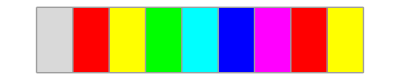
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ABCDEFGHI"}]
```

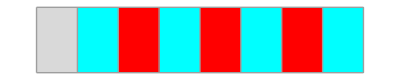
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ACDEFGHI"},2] (* Fixed so it doesn't take less than 2 colors, default is 6,  Note: color 0 = LightGray, not part of the cycle if colors are repeated! *)
```

```mathematica
SSSNewRule[{"ABA"->"AAB","A"->"ABA"}]
```

{s[{0,lhsTag$2946_},{1,lhsTag$2947_},{0,lhsTag$2948_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$2946,lhsTag$2947,lhsTag$2948}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$2950_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$2950}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}

Create and initialize a sessie object, look at different fields, use SSSSingleStep, SSSEvolve, SSSDisplay on it:

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A"];
Normal[sss]//Column
```

Net→{}
OutDegreePotential→{3}
OutDegreeRemaining→{3}
OutDegreeActual→{0}
InDegree→{1}
ConnectionList→{{1}→{2,3,4}}
Verdict→OK
RulesUsed→{2}
CellsDeleted→{{1}}
Distance→{0}
MaxColor→6
TagIndex→5
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}]}
Evolution→{A,ABA}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$2957_},{1,lhsTag$2958_},{0,lhsTag$2959_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$2957,lhsTag$2958,lhsTag$2959}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$2961_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$2961}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
{sss["TagIndex"],sss["Evolution"]}
```

{5,{A,ABA}}

```mathematica
sss=SSSSingleStep[sss];
{sss["TagIndex"],sss["Evolution"]}
```

{8,{A,ABA,AAB}}

```mathematica
sss=SSSEvolve[sss,50];
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB,ABAAAAAAAAABBBBBBBB,AABAAAAAAAABBBBBBBB,AAABAAAAAAABBBBBBBB,AAAABAAAAAABBBBBBBB,AAAAABAAAAABBBBBBBB,AAAAAABAAAABBBBBBBB,AAAAAAABAAABBBBBBBB,AAAAAAAABAABBBBBBBB}

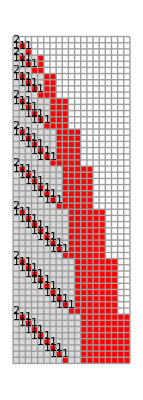


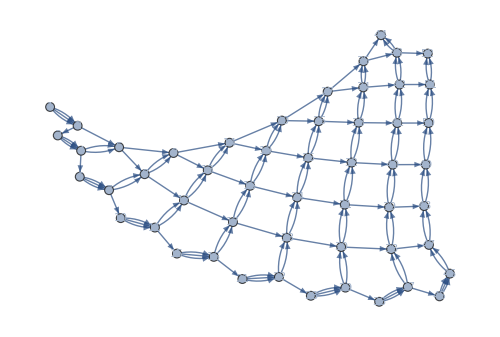
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,NetSize->500]
```

Normal way to create, evolve, and display a sessie object:

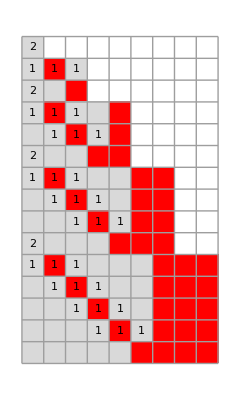
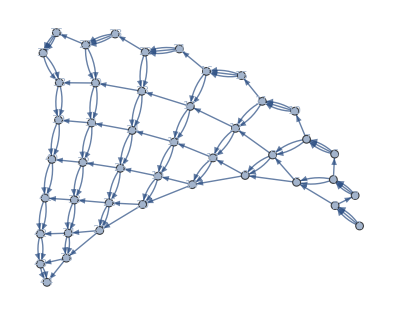
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15,NetMethod->GraphPlot];
```

Create another SSS without erasing the first one:

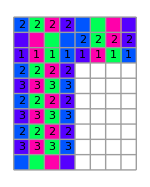
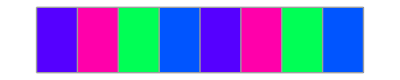
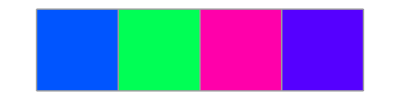
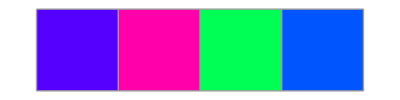
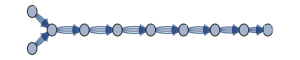
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
mirosessie = SSS[{"ORIMORIM" -> "MIRO", "MIRO" -> "ORIM", "ORIM" -> "MIRO"}, "MIROMIRO", 10, SSSMax -> 10, NetMethod -> GraphPlot, SSSSize->150,NetSize->300];
```

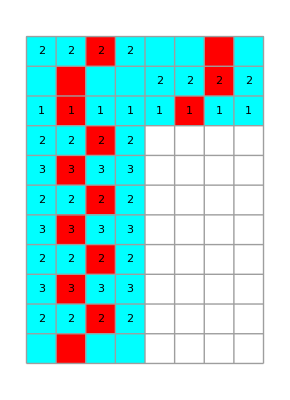
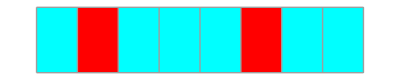
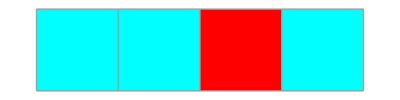
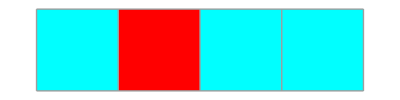
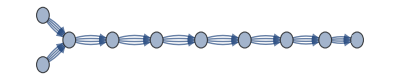
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
AssociateTo[mirosessie, "MaxColor" ->2];  (* colors will now recur, modulo-2: *)
SSSDisplay[mirosessie,NetSize->400]
```

```mathematica
mirosessie["Verdict"]
mirosessie["Evolution"]
mirosessie["MaxColor"]
```

Repeating

{MIROMIRO,ORIMMIRO,ORIMORIM,MIRO,ORIM,MIRO,ORIM,MIRO,ORIM,MIRO,ORIM}

2

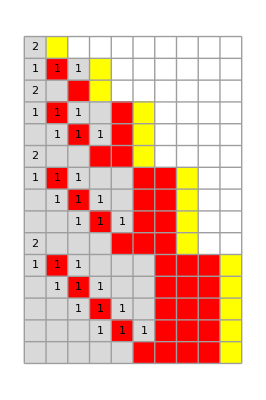
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2=SSS[{"ABA"->"AAB","A"->"ABA"}, "AC",44,SSSMax->15,NetMethod->GraphPlot];
```

Both sss and sss2 exist independently:

```mathematica
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB}

```mathematica
sss2["Evolution"]
```

{AC,ABAC,AABC,ABAABC,AABABC,AAABBC,ABAAABBC,AABAABBC,AAABABBC,AAAABBBC,ABAAAABBBC,AABAAABBBC,AAABAABBBC,AAAABABBBC,AAAAABBBBC,ABAAAAABBBBC,AABAAAABBBBC,AAABAAABBBBC,AAAABAABBBBC,AAAAABABBBBC,AAAAAABBBBBC,ABAAAAAABBBBBC,AABAAAAABBBBBC,AAABAAAABBBBBC,AAAABAAABBBBBC,AAAAABAABBBBBC,AAAAAABABBBBBC,AAAAAAABBBBBBC,ABAAAAAAABBBBBBC,AABAAAAAABBBBBBC,AAABAAAAABBBBBBC,AAAABAAAABBBBBBC,AAAAABAAABBBBBBC,AAAAAABAABBBBBBC,AAAAAAABABBBBBBC,AAAAAAAABBBBBBBC,ABAAAAAAAABBBBBBBC,AABAAAAAAABBBBBBBC,AAABAAAAAABBBBBBBC,AAAABAAAAABBBBBBBC,AAAAABAAAABBBBBBBC,AAAAAABAAABBBBBBBC,AAAAAAABAABBBBBBBC,AAAAAAAABABBBBBBBC,AAAAAAAAABBBBBBBBC}

Use SSSInteractiveDisplay to tweak the display options:

```mathematica
SSSInteractiveDisplay[sss]
```

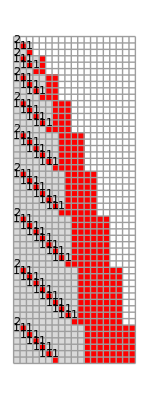
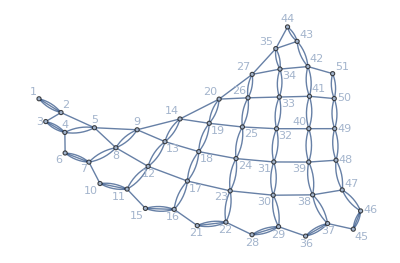
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,Min->1,Max->51,SSSMin->Automatic,SSSMax->Automatic,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->350,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,10.},VertexSize->Automatic,VertexLabels->Automatic,DirectedEdges->False]
```

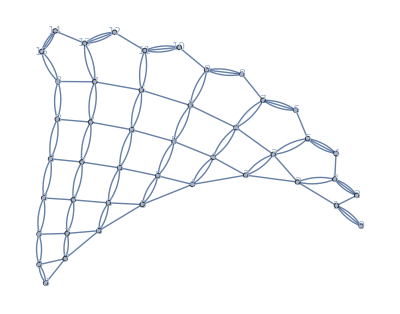

```mathematica
SSSDisplay[sss,Min->1,Max->51,SSSMin->Automatic,SSSMax->Automatic,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot,NoSSS},ImageSize->217.,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,10.},VertexSize->Automatic,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False]
```

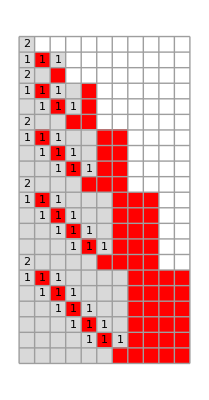
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,Min->1,Max->44,SSSMin->Automatic,SSSMax->21,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->198.,NetSize->{Automatic,342.},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False]
```

Examples of using SSSAnimate:

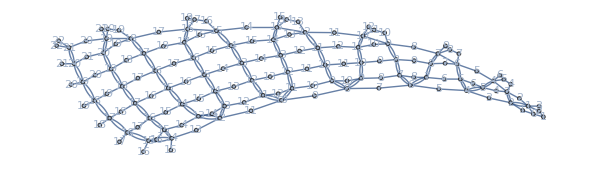

```mathematica
sss3=SSS[{"BAB"->"ABA","A"->"B","B"->"AA"},"BAB",150,NetSize->600,
NetMethod->{GraphPlot,NoSSS},
VertexSize->Automatic,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False];
```

```mathematica
SSSAnimate[sss3]
```

```mathematica
SSSAnimate[sss3,VertexLabels->"VertexWeight"]
```

```mathematica
SSSInitialState[{"ABA"->"AAB","BB"->"ABA"}]
```

ABABBABB

```mathematica
SSSInitialState[{"ABA"->"AAB","A"->"ABA","CDE"->""}]
```

ABABACDCECDCDECEDCEDEDEC

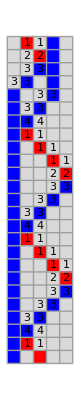


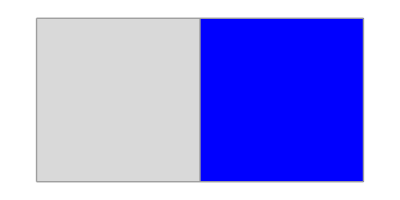
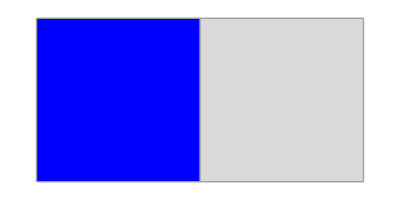
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[2168704802144169502244628730,80,SSSMax->25,NetSize->500,VertexLabels->None];
```

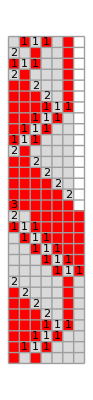
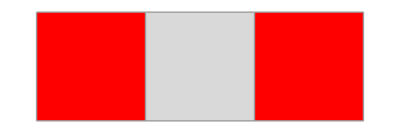
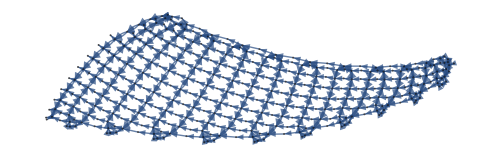
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[36660528645,400,SSSMax->30,NetSize->500,VertexLabels->Placed["Name",Tooltip]];
```

Let's look at both the reduced enumeration index and the quinary code of the mirosessie ruleset!  😁

```mathematica
FromReducedRankRuleSet[mirosessie["RuleSet"]]
```

{31724272965613982509673497002743933689002475059552671099609208860239348964268003480421701342935661158978046841164354624000010772998214031024664456344795268591236103093181099442783233154578546344891700474079141153768283931377232895645890131629585061455145478242492675781,444444444444443444444444444444443444444443444444444444344444444444444344444444444444444344444444344444444444424444444444443444444443444444444444444443444444444444442444444444444344444444344444444444444444344444444444444244444444444444344444444444444444344444444344444444444424444444444444434444444444444444434444444434444444444442444444444444344444444344444444444444444344444444444444,{ORIMORIM→MIRO,MIRO→ORIM,ORIM→MIRO}}

Other enumeration examples:

```mathematica
FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"A"}]//InputForm
```

{236252479, "324323423242", {"AA" -> "BA", "AB" -> "AA", "B" -> "A"}}

```mathematica
FromReducedRankIndex[236252479]
```

{236252479,324323423242,{AA→BA,AB→AA,B→A}}

```mathematica
FromReducedRankQuinaryCode["324323423242"]
```

{236252479,324323423242,{AA→BA,AB→AA,B→A}}

```mathematica
FromReducedRankRuleSet[{"BAB"->"ABA","A"->"B","B"->"AA"}]
```

{36660528645,433423432242423,{BAB→ABA,A→B,B→AA}}

```mathematica
FromReducedRankIndex/@ Range[25]
```

{{1,,{A→}},{2,0,{A→,→A}},{3,1,{A→,A→}},{4,2,{A→A}},{5,3,{AA→}},{6,4,{B→}},{7,00,{A→,→A,→,A→}},{8,01,{A→,→A,→A}},{9,02,{A→,→A,A→}},{10,03,{A→,→AA}},{11,04,{A→,→B}},{12,10,{A→,A→,→A}},{13,11,{A→,A→,A→}},{14,12,{A→,A→A}},{15,13,{A→,AA→}},{16,14,{A→,B→}},{17,20,{A→A,→,A→}},{18,21,{A→A,→A}},{19,22,{A→A,A→}},{20,23,{A→AA}},{21,24,{A→B}},{22,30,{AA→,→A}},{23,31,{AA→,A→}},{24,32,{AA→A}},{25,33,{AAA→}}}

```mathematica
Grid[
Prepend[
FromReducedRankIndex/@ Range[50],
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
1 |  | {A→}
2 | 0 | {A→,→A}
3 | 1 | {A→,A→}
4 | 2 | {A→A}
5 | 3 | {AA→}
6 | 4 | {B→}
7 | 00 | {A→,→A,→,A→}
8 | 01 | {A→,→A,→A}
9 | 02 | {A→,→A,A→}
10 | 03 | {A→,→AA}
11 | 04 | {A→,→B}
12 | 10 | {A→,A→,→A}
13 | 11 | {A→,A→,A→}
14 | 12 | {A→,A→A}
15 | 13 | {A→,AA→}
16 | 14 | {A→,B→}
17 | 20 | {A→A,→,A→}
18 | 21 | {A→A,→A}
19 | 22 | {A→A,A→}
20 | 23 | {A→AA}
21 | 24 | {A→B}
22 | 30 | {AA→,→A}
23 | 31 | {AA→,A→}
24 | 32 | {AA→A}
25 | 33 | {AAA→}
26 | 34 | {AB→}
27 | 40 | {B→,→A}
28 | 41 | {B→,A→}
29 | 42 | {B→A}
30 | 43 | {BA→}
31 | 44 | {C→}
32 | 000 | {A→,→A,→,A→,→A}
33 | 001 | {A→,→A,→,A→,A→}
34 | 002 | {A→,→A,→,A→A}
35 | 003 | {A→,→A,→,AA→}
36 | 004 | {A→,→A,→,B→}
37 | 010 | {A→,→A,→A,→,A→}
38 | 011 | {A→,→A,→A,→A}
39 | 012 | {A→,→A,→A,A→}
40 | 013 | {A→,→A,→AA}
41 | 014 | {A→,→A,→B}
42 | 020 | {A→,→A,A→,→A}
43 | 021 | {A→,→A,A→,A→}
44 | 022 | {A→,→A,A→A}
45 | 023 | {A→,→A,AA→}
46 | 024 | {A→,→A,B→}
47 | 030 | {A→,→AA,→,A→}
48 | 031 | {A→,→AA,→A}
49 | 032 | {A→,→AA,A→}
50 | 033 | {A→,→AAA}

```mathematica
FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

{1181262395,3243234232423,{AA→BA,AB→AA,B→AA}}

```mathematica
Grid[
Prepend[
FromReducedRankIndex/@ (1181262395+Range[0,25]),
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
1181262395 | 3243234232423 | {AA→BA,AB→AA,B→AA}
1181262396 | 3243234232424 | {AA→BA,AB→AA,B→B}
1181262397 | 3243234232430 | {AA→BA,AB→AA,BA→,→A}
1181262398 | 3243234232431 | {AA→BA,AB→AA,BA→,A→}
1181262399 | 3243234232432 | {AA→BA,AB→AA,BA→A}
1181262400 | 3243234232433 | {AA→BA,AB→AA,BAA→}
1181262401 | 3243234232434 | {AA→BA,AB→AA,BB→}
1181262402 | 3243234232440 | {AA→BA,AB→AA,C→,→A}
1181262403 | 3243234232441 | {AA→BA,AB→AA,C→,A→}
1181262404 | 3243234232442 | {AA→BA,AB→AA,C→A}
1181262405 | 3243234232443 | {AA→BA,AB→AA,CA→}
1181262406 | 3243234232444 | {AA→BA,AB→AA,D→}
1181262407 | 3243234233000 | {AA→BA,AB→AAA,→,A→,→A,→,A→}
1181262408 | 3243234233001 | {AA→BA,AB→AAA,→,A→,→A,→A}
1181262409 | 3243234233002 | {AA→BA,AB→AAA,→,A→,→A,A→}
1181262410 | 3243234233003 | {AA→BA,AB→AAA,→,A→,→AA}
1181262411 | 3243234233004 | {AA→BA,AB→AAA,→,A→,→B}
1181262412 | 3243234233010 | {AA→BA,AB→AAA,→,A→,A→,→A}
1181262413 | 3243234233011 | {AA→BA,AB→AAA,→,A→,A→,A→}
1181262414 | 3243234233012 | {AA→BA,AB→AAA,→,A→,A→A}
1181262415 | 3243234233013 | {AA→BA,AB→AAA,→,A→,AA→}
1181262416 | 3243234233014 | {AA→BA,AB→AAA,→,A→,B→}
1181262417 | 3243234233020 | {AA→BA,AB→AAA,→,A→A,→,A→}
1181262418 | 3243234233021 | {AA→BA,AB→AAA,→,A→A,→A}
1181262419 | 3243234233022 | {AA→BA,AB→AAA,→,A→A,A→}
1181262420 | 3243234233023 | {AA→BA,AB→AAA,→,A→AA}

Examples of RuleSet Tests:

```mathematica
FromReducedRankQuinaryCode["3432334234312343"]
TestForConflictingRules[%]
```

{158448842380,3432334234312343,{ABA→AAB,ABA→,A→ABA}}

{158448843907,3432334234340000,{ABA→AAB,ABB→,→A,→,A→,→A,→,A→}}

```mathematica
FromReducedRankQuinaryCode["24344234244"]
TestForConflictingRules[%]
```

{41106356,24344234244,{A→BC,AB→C}}

{41106407,24344240000,{A→BC,B→,→A,→,A→,→A,→,A→}}

```mathematica
Grid[
Prepend[
FromReducedRankIndex/@ (41106356+Range[0,51]),
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
41106356 | 24344234244 | {A→BC,AB→C}
41106357 | 24344234300 | {A→BC,ABA→,→A,→,A→}
41106358 | 24344234301 | {A→BC,ABA→,→A,→A}
41106359 | 24344234302 | {A→BC,ABA→,→A,A→}
41106360 | 24344234303 | {A→BC,ABA→,→AA}
41106361 | 24344234304 | {A→BC,ABA→,→B}
41106362 | 24344234310 | {A→BC,ABA→,A→,→A}
41106363 | 24344234311 | {A→BC,ABA→,A→,A→}
41106364 | 24344234312 | {A→BC,ABA→,A→A}
41106365 | 24344234313 | {A→BC,ABA→,AA→}
41106366 | 24344234314 | {A→BC,ABA→,B→}
41106367 | 24344234320 | {A→BC,ABA→A,→,A→}
41106368 | 24344234321 | {A→BC,ABA→A,→A}
41106369 | 24344234322 | {A→BC,ABA→A,A→}
41106370 | 24344234323 | {A→BC,ABA→AA}
41106371 | 24344234324 | {A→BC,ABA→B}
41106372 | 24344234330 | {A→BC,ABAA→,→A}
41106373 | 24344234331 | {A→BC,ABAA→,A→}
41106374 | 24344234332 | {A→BC,ABAA→A}
41106375 | 24344234333 | {A→BC,ABAAA→}
41106376 | 24344234334 | {A→BC,ABAB→}
41106377 | 24344234340 | {A→BC,ABB→,→A}
41106378 | 24344234341 | {A→BC,ABB→,A→}
41106379 | 24344234342 | {A→BC,ABB→A}
41106380 | 24344234343 | {A→BC,ABBA→}
41106381 | 24344234344 | {A→BC,ABC→}
41106382 | 24344234400 | {A→BC,AC→,→A,→,A→}
41106383 | 24344234401 | {A→BC,AC→,→A,→A}
41106384 | 24344234402 | {A→BC,AC→,→A,A→}
41106385 | 24344234403 | {A→BC,AC→,→AA}
41106386 | 24344234404 | {A→BC,AC→,→B}
41106387 | 24344234410 | {A→BC,AC→,A→,→A}
41106388 | 24344234411 | {A→BC,AC→,A→,A→}
41106389 | 24344234412 | {A→BC,AC→,A→A}
41106390 | 24344234413 | {A→BC,AC→,AA→}
41106391 | 24344234414 | {A→BC,AC→,B→}
41106392 | 24344234420 | {A→BC,AC→A,→,A→}
41106393 | 24344234421 | {A→BC,AC→A,→A}
41106394 | 24344234422 | {A→BC,AC→A,A→}
41106395 | 24344234423 | {A→BC,AC→AA}
41106396 | 24344234424 | {A→BC,AC→B}
41106397 | 24344234430 | {A→BC,ACA→,→A}
41106398 | 24344234431 | {A→BC,ACA→,A→}
41106399 | 24344234432 | {A→BC,ACA→A}
41106400 | 24344234433 | {A→BC,ACAA→}
41106401 | 24344234434 | {A→BC,ACB→}
41106402 | 24344234440 | {A→BC,AD→,→A}
41106403 | 24344234441 | {A→BC,AD→,A→}
41106404 | 24344234442 | {A→BC,AD→A}
41106405 | 24344234443 | {A→BC,ADA→}
41106406 | 24344234444 | {A→BC,AE→}
41106407 | 24344240000 | {A→BC,B→,→A,→,A→,→A,→,A→}

```mathematica
FromReducedRankQuinaryCode["434422434424224"]
TestForConflictingRules[%]
```

{36902752596,434422434424224,{BC→A,BC→B,A→B}}

{36902753282,434422434440000,{BC→A,BD→,→A,→,A→,→A,→,A→}}

```mathematica
FromReducedRankQuinaryCode["24144124234"]
TestForConflictingRules[%]
```

{40321351,24144124234,{A→B,→C,→A,B→AB}}

{40328125,24144333333,{A→B,→CAAAAAA}}

```mathematica
FromReducedRankQuinaryCode["2414434124234"]
TestForConflictingRules[%]
```

{1008211976,2414434124234,{A→B,→CB,→A,B→AB}}

{1008218750,2414434333333,{A→B,→CBAAAAAA}}

```mathematica
FromReducedRankIndex[321351]
TestForConflictingRules[%]
```

{321351,24124234,{A→B,→A,B→AB}}

{321875,24133333,{A→B,→AAAAAA}}

```mathematica
FromReducedRankIndex[8065101]
TestForConflictingRules[%]
```

{8065101,2414424234,{A→B,→C,B→AB}}

{8065625,2414433333,{A→B,→CAAAAA}}

```mathematica
FromReducedRankIndex[40321351]
TestForConflictingRules[%]
```

{40321351,24144124234,{A→B,→C,→A,B→AB}}

{40328125,24144333333,{A→B,→CAAAAAA}}

```mathematica
FromReducedRankIndex[40328125]
TestForConflictingRules[%]
```

{40328125,24144333333,{A→B,→CAAAAAA}}

{}

```mathematica
FromReducedRankIndex[13267]
TestForConflictingRules[%]
```

{13267,244420,{A→D,A→,→A}}

{13271,244424,{A→D,B→}}

## Testing next function to add: